```mathematica
<<FeynCalc`
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

## ϕχχ → χχ (Higgs Portal, Majorana χ)

```mathematica
(* phi(k1) chi(k2) chi(k3) -> chi(p1) chi(p2) *)
(* 16 diagrams: 8 direct + 8 exchange (p1<->p2) *)

FCClearScalarProducts[];

SP[k1,k1]=mY^2; SP[k2,k2]=mX^2;
SP[k3,k3]=mX^2; SP[p1,p1]=mX^2; SP[p2,p2]=mX^2;

SP[k1,k2]=(s12-mY^2-mX^2)/2;
SP[k1,k3]=(s13-mY^2-mX^2)/2;
SP[k1,p1]=(mY^2+mX^2-t1)/2;
SP[k2,p1]=(2 mX^2-t2)/2;
SP[k3,p1]=(2 mX^2-t3)/2;

SP[k2,k3]=-(s12-mY^2-mX^2)/2-(s13-mY^2-mX^2)/2+(mY^2+mX^2-t1)/2+(2 mX^2-t2)/2+(2 mX^2-t3)/2-(mY^2+2 mX^2)/2;

SP[p2,k1]=SP[k1,k1]+SP[k1,k2]+SP[k1,k3]-SP[k1,p1];
SP[p2,k2]=SP[k1,k2]+SP[k2,k2]+SP[k2,k3]-SP[k2,p1];
SP[p2,k3]=SP[k1,k3]+SP[k2,k3]+SP[k3,k3]-SP[k3,p1];
SP[p2,p1]=SP[k1,p1]+SP[k2,p1]+SP[k3,p1]-SP[p1,p1];

sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
EXf=sqrtsNR/2;
NRrules={s12->(mY+mX)^2, s13->(mY+mX)^2, t1->mY^2+mX^2-2 mY EXf, t2->2 mX^2-2 mX EXf, t3->2 mX^2-2 mX EXf};

V=lams+I lamp GA[5];
```

```mathematica
(* S1: incoming s-channel phi, outgoing chi propagator *)
qPhi1=k2+k3; PX1=k2+k3-p1;
DenPhi1=ExpandScalarProduct[SP[qPhi1,qPhi1]]-mY^2;
DenX1=ExpandScalarProduct[SP[PX1,PX1]]-mX^2;
amp1=(SpinorVBar[k2,mX].V.SpinorU[k3,mX] * SpinorUBar[p2,mX].V.(GS[PX1]+mX).V.SpinorV[p1,mX])/(DenPhi1 DenX1)//DiracSimplify;

(* S2: incoming s-channel phi, k1-p1 chi propagator *)
qPhi2=k2+k3; PX2=k1-p1;
DenPhi2=ExpandScalarProduct[SP[qPhi2,qPhi2]]-mY^2;
DenX2=ExpandScalarProduct[SP[PX2,PX2]]-mX^2;
amp2=(SpinorVBar[k2,mX].V.SpinorU[k3,mX] * SpinorUBar[p2,mX].V.(GS[PX2]+mX).V.SpinorV[p1,mX])/(DenPhi2 DenX2)//DiracSimplify;

(* S3: outgoing s-channel phi, k1+k3 chi propagator *)
qPhi3=p1+p2; PX3=k1+k3;
DenPhi3=ExpandScalarProduct[SP[qPhi3,qPhi3]]-mY^2;
DenX3=ExpandScalarProduct[SP[PX3,PX3]]-mX^2;
amp3=(SpinorVBar[k2,mX].V.(GS[PX3]+mX).V.SpinorU[k3,mX] * SpinorUBar[p2,mX].V.SpinorV[p1,mX])/(DenPhi3 DenX3)//DiracSimplify;

(* S4: outgoing s-channel phi, -(k1+k2) chi propagator *)
qPhi4=p1+p2; PX4=-(k1+k2);
DenPhi4=ExpandScalarProduct[SP[qPhi4,qPhi4]]-mY^2;
DenX4=ExpandScalarProduct[SP[PX4,PX4]]-mX^2;
amp4=(SpinorVBar[k2,mX].V.(GS[PX4]+mX).V.SpinorU[k3,mX] * SpinorUBar[p2,mX].V.SpinorV[p1,mX])/(DenPhi4 DenX4)//DiracSimplify;

(* T1: diagram 5 *)
qPhi5=k2-p1; PX5=k2+k3-p1;
DenPhi5=ExpandScalarProduct[SP[qPhi5,qPhi5]]-mY^2;
DenX5=ExpandScalarProduct[SP[PX5,PX5]]-mX^2;
amp5=(SpinorUBar[p2,mX].V.(GS[PX5]+mX).V.SpinorU[k3,mX] * SpinorVBar[k2,mX].V.SpinorV[p1,mX])/(DenPhi5 DenX5)//DiracSimplify;

(* T2: diagram 6 *)
qPhi6=k3-p2; PX6=-(k1+k2);
DenPhi6=ExpandScalarProduct[SP[qPhi6,qPhi6]]-mY^2;
DenX6=ExpandScalarProduct[SP[PX6,PX6]]-mX^2;
amp6=(SpinorUBar[p2,mX].V.SpinorU[k3,mX] * SpinorVBar[k2,mX].V.(GS[PX6]+mX).V.SpinorV[p1,mX])/(DenPhi6 DenX6)//DiracSimplify;

(* T3: diagram 7 *)
qPhi7=k3-p2; PX7=k1+k3;
DenPhi7=ExpandScalarProduct[SP[qPhi7,qPhi7]]-mY^2;
DenX7=ExpandScalarProduct[SP[PX7,PX7]]-mX^2;
amp7=(SpinorUBar[p2,mX].V.(GS[PX7]+mX).V.SpinorU[k3,mX] * SpinorVBar[k2,mX].V.SpinorV[p1,mX])/(DenPhi7 DenX7)//DiracSimplify;

(* T4: diagram 8 *)
qPhi8=k2-p1; PX8=k1-p1;
DenPhi8=ExpandScalarProduct[SP[qPhi8,qPhi8]]-mY^2;
DenX8=ExpandScalarProduct[SP[PX8,PX8]]-mX^2;
amp8=(SpinorVBar[k2,mX].V.(GS[PX8]+mX).V.SpinorV[p1,mX] * SpinorUBar[p2,mX].V.SpinorU[k3,mX])/(DenPhi8 DenX8)//DiracSimplify;

(* Exchange amplitudes: p1 <-> p2 *)
swapMomenta[expr_]:=expr/.p1->ptmp/.{p2->p1,ptmp->p2};
amp9=swapMomenta[amp1]; amp10=swapMomenta[amp2]; amp11=swapMomenta[amp3]; amp12=swapMomenta[amp4];
amp13=swapMomenta[amp5]; amp14=swapMomenta[amp6]; amp15=swapMomenta[amp7]; amp16=swapMomenta[amp8];

(* Signs: {+1,+1,+1,+1,-1,-1,-1,-1,-1,-1,-1,-1,+1,+1,+1,+1} *)
amps={amp1,amp2,amp3,amp4,-amp5,-amp6,-amp7,-amp8,-amp9,-amp10,-amp11,-amp12,amp13,amp14,amp15,amp16};
```

```mathematica
proc[i_,j_]:=Module[{cc,Mij},
 cc=ComplexConjugate[amps⟦j⟧]/.{Conjugate[lams]->lams,Conjugate[lamp]->lamp};
 Mij=FermionSpinSum[amps⟦i⟧ cc]//Contract//DiracSimplify;
 Mij=Mij/.NRrules;
 Mij=Mij/.Eps[__]->0;
 Mij=PowerExpand[Mij]/.mY->mX/r//FullSimplify
];
```

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_hP_v2"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];
```

```mathematica
Do[Print["(",i,",",i,") ..."];
 term=proc[i,i];
 Put[term,FileNameJoin[{outputDir,"diag_"<>ToString[i]<>"_"<>ToString[i]<>".m"}]];
 Clear[term]; Print["  Done."];
,{i,1,16}];

Do[Print["i = ",i," ..."];
 Do[
 term=2 proc[i,j];
 Put[term,FileNameJoin[{outputDir,"offdiag_"<>ToString[i]<>"_"<>ToString[j]<>".m"}]];
 Clear[term];
 ,{j,i+1,16}];
 Print["  Done with i = ",i,"."];
,{i,1,16}];

Print["\nAll 136 terms saved to: ",outputDir];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(7,7) ...

Done.

(8,8) ...

Done.

(9,9) ...

Done.

(10,10) ...

Done.

(11,11) ...

Done.

(12,12) ...

Done.

(13,13) ...

Done.

(14,14) ...

Done.

(15,15) ...

Done.

(16,16) ...

Done.

i = 1 ...

Done with i = 1.

i = 2 ...

Done with i = 2.

i = 3 ...

Done with i = 3.

i = 4 ...

Done with i = 4.

i = 5 ...

Done with i = 5.

i = 6 ...

Done with i = 6.

i = 7 ...

Done with i = 7.

i = 8 ...

Done with i = 8.

i = 9 ...

Done with i = 9.

i = 10 ...

Done with i = 10.

i = 11 ...

Done with i = 11.

i = 12 ...

Done with i = 12.

i = 13 ...

Done with i = 13.

i = 14 ...

Done with i = 14.

i = 15 ...

Done with i = 15.

i = 16 ...

Done with i = 16.

All 136 terms saved to: /home/gab/Desktop/PyCharm_env/secluded_DM/mathematica/MsqTerms_YXX_XX_hP_v2

## Load and sum

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_hP_v2"}];
files=FileNames["*.m",outputDir];
Print["Loading ",Length[files]," terms..."];
MsqTotal=0;
Do[term=Get[f]; MsqTotal+=term; Clear[term];,{f,files}];
MsqAvgNR=MsqTotal/4//Simplify;
```

Loading 136 terms...

```mathematica
MsqAvgNR//FullSimplify
```

1/(mX^2 (1+r-4 r^2-4 r^3)^2)r^2 (lamp^6 (1-2 r)^2 (1+4 r)^3+lams^6 (-1-4 r+4 r^2+16 r^3)^2+lamp^2 lams^4 (1+4 r) (3+4 r (3+r (9+8 r (1+r) (-1+8 r))))+lamp^4 lams^2 (3+8 r (3+2 r (5+r (6+r (25+16 r (7+4 r)))))))

```mathematica
sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2 a b-2 a c-2 b c;
lambdaNR=Kallen[sNR,mX^2,mX^2]/.mY->mX/r//Simplify;

sigmav2NR=MsqAvgNR*Sqrt[lambdaNR]/(64 Pi mY mX^2 sNR);
sigmav2NR=PowerExpand[sigmav2NR]/.mY->mX/r//FullSimplify;

(* Delta_2: sigmav2 = Delta_2 / mX^5 *)
Delta2=PowerExpand[sigmav2NR*mX^5]//FullSimplify;
Print["\nDelta_2(r, lams, lamp) = ",Delta2];

(* Special cases *)
Delta2scalar=Delta2/.lamp->0//FullSimplify;
Print["Delta_2 (scalar only) = ",Delta2scalar];
Delta2pseudo=Delta2/.lams->0//FullSimplify;
Print["Delta_2 (pseudo only) = ",Delta2pseudo];
```

Delta_2(r, lams, lamp) = 1/(64 π (1+2 r)^3 (-1+r+2 r^2)^2)r^3 √(1+4 r) (lamp^6 (1-2 r)^2 (1+4 r)^3+lams^6 (-1-4 r+4 r^2+16 r^3)^2+lamp^2 lams^4 (1+4 r) (3+4 r (3+r (9+8 r (1+r) (-1+8 r))))+lamp^4 lams^2 (3+8 r (3+2 r (5+r (6+r (25+16 r (7+4 r)))))))

Delta_2 (scalar only) = (lams^6 r^3 (1+4 r)^(5/2))/(64 (1+r)^2 (π+2 π r))

Delta_2 (pseudo only) = (lamp^6 r^3 (1+4 r)^(7/2))/(64 π (1+r)^2 (1+2 r)^3)

```mathematica
Print["\n--- Delta_2(r) for lams=1, lamp=0 ---"];
N[Delta2scalar/.{lams->1,r->1}]
N[Delta2scalar/.{lams->1,r->2}]
N[Delta2scalar/.{lams->1,r->5}]
N[Delta2scalar/.{lams->1,r->10}]
```

--- Delta_2(r) for lams=1, lamp=0 ---

0.0231694

0.214859

3.17273

21.0681

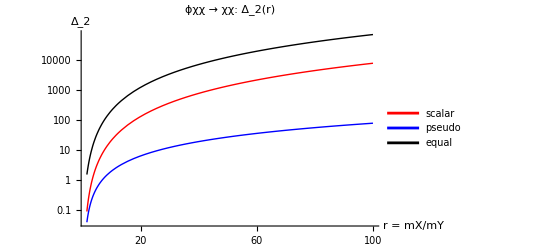

```mathematica
Plot[{Delta2/.{lams->1,lamp->0}, Delta2/.{lams->0,lamp->1}, Delta2/.{lams->1,lamp->1}}, {r, 1.5, 100},
 PlotRange -> All,
 ScalingFunctions -> {"Linear", "Log"},
 AxesLabel -> {"r = mX/mY", "Δ_2"},
 PlotLabel -> "ϕχχ → χχ:  Δ_2(r)",
 PlotStyle -> {{Thick, Red}, {Thick, Blue}, {Thick, Black}},
 PlotLegends -> {"scalar", "pseudo", "equal"}]
```